```mathematica
stream=OpenRead["realfxptsprecision1000no1"];
ls=ReadList[stream];
Close[stream]
```

realfxptsprecision1000no1

```mathematica
Length[ls]
```

200

```mathematica
Clear[list];
stream1=OpenRead["realfxNrhoNrun1jun16no11"];
list=ReadList[stream1];
Close[stream1]
```

realfxNrhoNrun1jun16no11

```mathematica
Length[list]
```

1000

```mathematica
precision=1000;
meanerrors={};
For[n=0,n<50,n++;

backorbit={};
fx=ls[[n,2]];
For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=Append[backorbit,list[[a,3]]]
](* if loop *)

];(* For loop *)

relerrors={};
For[

k=0,k<Length[backorbit],k++;
zr=backorbit[[k]];
ds=zr-fx;
If[ds!=0,
logdistance=Re[Log[Abs[ds]]];
m=meansslopes[[n,2]];
b=meansintercepts[[n,2]];
estimate=k*m+b;
error=logdistance-estimate;
relerror=Abs[error/logdistance];
relerrors=Append[relerrors,relerror]]

];(* k loop *)
mxe=Log[Mean[relerrors]]; (* n.b. : log scaling *)
meanerrors=Append[meanerrors,mxe];
]; (* n loop *)
Print["mean errors"];
Print[ListPlot[meanerrors]]
```

## leaf6point4left

mean errors

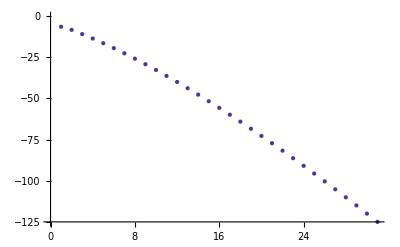

max errors

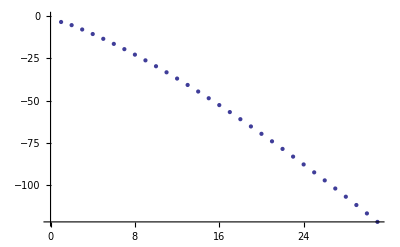

```mathematica
precision=1000;
worsterrors={};
For[n=0,n<50,n++;

backorbit={};
fx=ls[[n,2]];
For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=Append[backorbit,list[[a,3]]]
](* if loop *)

];(* For loop *)

relerrors={};
For[

k=0,k<Length[backorbit],k++;
zr=backorbit[[k]];
ds=zr-fx;
If[ds!=0,
logdistance=Re[Log[Abs[ds]]];
m=meansslopes[[n,2]];
b=meansintercepts[[n,2]];
estimate=k*m+b;
error=logdistance-estimate;
relerror=Abs[error/logdistance];
relerrors=Append[relerrors,relerror]]

];(* k loop *)
mxe=Log[Max[relerrors]]; (* n.b. : log scaling *)
worsterrors=Append[worsterrors,mxe];
]; (* n loop *)
Print["max errors"];
Print[ListPlot[worsterrors]]


leaf6point4right
```